```mathematica
1+1
```

2

```mathematica
fD1 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D1_v1.csv"];
fD2 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D2_v1.csv"];
fD1 = Flatten@fD1;
fD2 = Flatten@fD2;
```

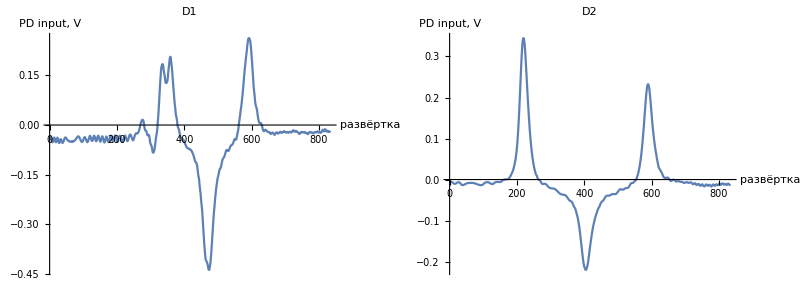

```mathematica
scale = 240;
image = Multicolumn[{
ListPlot[fD1, PlotRange->Full, Joined->True, ImageSize->{scale, scale}, AspectRatio->1,
PlotLabel->"D1", AxesLabel->{"развёртка", "PD input, V"}],
ListPlot[fD2, PlotRange->Full, Joined->True, ImageSize->{scale, scale}, AspectRatio->1,
PlotLabel->"D2", AxesLabel->{"развёртка", "PD input, V"}]
}]
```

```mathematica
(* отнормируем *)
αx = 10. /Length@fD1
xs =αx Range[Length@fD1] ;
data = Transpose[{xs, Flatten@fD1}];
```

0.0119904

```mathematica
color1 = RGBColor[0.27,0.25,1.]
```

RGBColor[0.27, 0.25, 1.]

## Подготовка

```mathematica
d1 = 200;
d2 = 400;
d3 = 550;
d4 = 650;
```

{a1→0.209984,x01→4.01515,σ1→0.0871442,a2→0.237633,x02→4.30228,σ2→0.123213,c→-0.0439162}

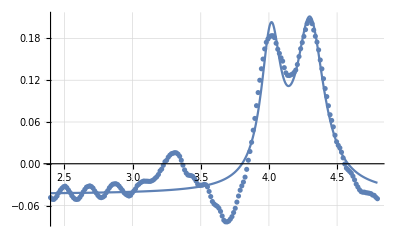

```mathematica
si = d1;
ei = d2;
fit = FindFit[data⟦si;;ei⟧, {a1 σ1^2/((x-x01)^2+σ1^2) +a2 σ2^2/((x-x02)^2+σ2^2) + c}, 
{{a1, 0.15}, {x01, 4}, {σ1, 0.12},{a2, 0.18}, {x02, 4.35}, {σ2, 0.12}, c}, x]
{aV11, x0V11, σV11, aV12, x0V12, σV12, cV1} = {a1, x01, σ1,a2, x02, σ2, c}/.fit;
f1[x_] := aV11 σV11^2/((x-x0V11)^2+σV11^2) +aV12 σV12^2/((x-x0V12)^2+σV12^2) + cV1;
Show[{
Plot[f1[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All, GridLines->Automatic],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

{a→-0.421719,x0→5.6481,σ→0.239563,c→-0.025222}

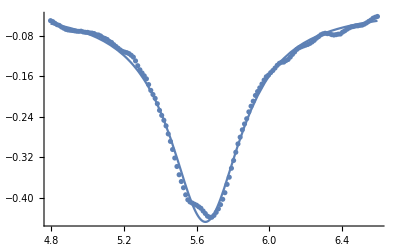

```mathematica
si = d2;
ei = d3;
fit = FindFit[data⟦si;;ei⟧, {a σ^2/((x-x0)^2+σ^2) + c}, {{a, -0.4}, {x0, 5.7}, {σ,0.5}, c}, x]
{aV2, x0V2, σV2, c2V2} = {a, x0, σ, c}/.fit;
f2[x_] := aV2 σV2^2/((x-x0V2)^2+σV2^2) + c2V2;
Show[{
Plot[f2[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

{a→0.332879,x0→7.09455,σ→0.196566,c2→-0.0628763}

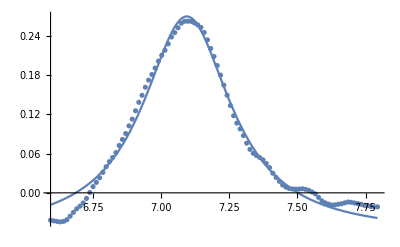

```mathematica
si = d3;
ei = d4;
fit = FindFit[data⟦si;;ei⟧, {a σ^2/((x-x0)^2+σ^2) + c2}, {{a, 0.37}, {x0, 7}, {σ, 0.135}, c2}, x]
{aV3, x0V3, σV3, c2V3} = {a, x0, σ, c2}/.fit;
f3[x_] := aV3 σV3^2/((x-x0V3)^2+σV3^2) + c2V3;
Show[{
Plot[f3[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

## Фит

{a11→0.206277,x011→4.01223,σ11→0.0849348,a12→0.242698,x012→4.30356,σ12→0.139852,a2→-0.412071,x02→5.64939,σ2→0.238696,a3→0.326803,x03→7.09091,σ3→0.18216,c→-0.041761}

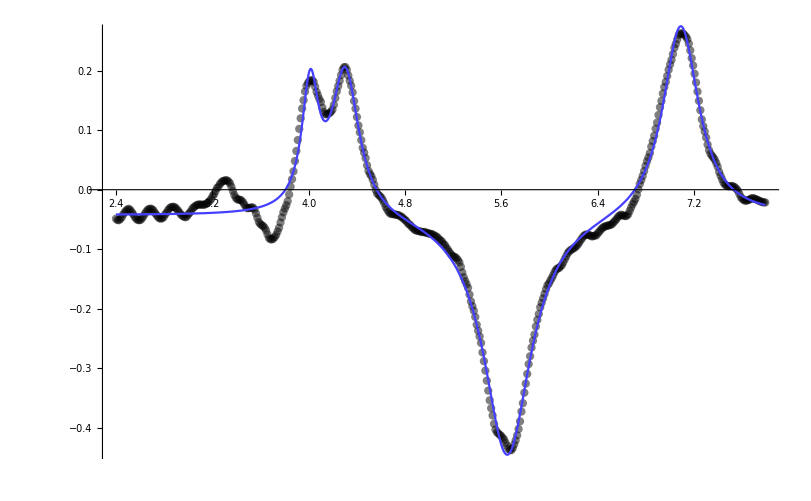

```mathematica
si = d1;
ei = d4;
nlm = NonlinearModelFit[data⟦si;;ei⟧, 
a11 σ11^2/((x-x011)^2+σ11^2)+a12 σ12^2/((x-x012)^2+σ12^2)+a2 σ2^2/((x-x02)^2+σ2^2)+a3 σ3^2/((x-x03)^2+σ3^2)+ c, 
{{a11, aV11}, {x011, x0V11}, {σ11, σV11},
{a12, aV12}, {x012, x0V12}, {σ12, σV12},
{a2, aV2}, {x02, x0V2}, {σ2,σV2},
{a3, aV3}, {x03, x0V3}, {σ3, σV3}, c},x];
fit0 = nlm["BestFitParameters"]
f0[x_] :=a11 σ11^2/((x-x011)^2+σ11^2)+a12 σ12^2/((x-x012)^2+σ12^2)+a2 σ2^2/((x-x02)^2+σ2^2)+a3 σ3^2/((x-x03)^2+σ3^2)+ c /. fit0;
im1 = Show[{
ListPlot[data⟦si;;ei⟧, PlotRange->All, Joined->False, PlotStyle->{Black, Opacity[0.5]}],
Plot[f0[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All, PlotStyle->color1]
}]
```

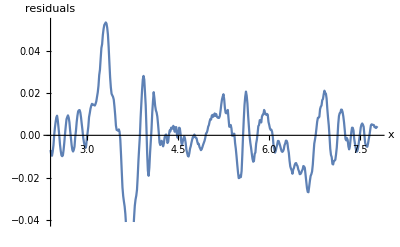

```mathematica
im2 = ListPlot[Transpose[{xs⟦si;;ei⟧,nlm["FitResiduals"]}], Joined->True, AxesLabel->{"x", "residuals"}, PlotRange->{{si αx, ei αx}, Automatic}]
```

```mathematica
nlm["ParameterTable"]
```

General::munfl: Exp[-1788.28] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1730.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2065.92] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a11 | 0.206277 | 0.00738613 | 27.9276 | 2.5542×10^-99
x011 | 4.01223 | 0.0032569 | 1231.92 | 0.
σ11 | 0.0849348 | 0.00562605 | 15.0967 | 9.26104×10^-42
a12 | 0.242698 | 0.00564481 | 42.9949 | 2.80999×10^-159
x012 | 4.30356 | 0.0039863 | 1079.59 | 0.
σ12 | 0.139852 | 0.00651023 | 21.4819 | 1.925×10^-70
a2 | -0.412071 | 0.00426979 | -96.5087 | 2.90367×10^-297
x02 | 5.64939 | 0.00243263 | 2322.34 | 0.
σ2 | 0.238696 | 0.0040549 | 58.866 | 3.6989×10^-210
a3 | 0.326803 | 0.00486156 | 67.2219 | 6.83803×10^-233
x03 | 7.09091 | 0.00267324 | 2652.56 | 0.
σ3 | 0.18216 | 0.00430804 | 42.2838 | 1.01538×10^-156
c | -0.041761 | 0.00156868 | -26.6217 | 1.40226×10^-93

## Обработка

```mathematica
Print["Отклонение CR: ", Abs@((x03 + (x011+x012)/2)/2 - x02)/x02 * 100 /. fit0, "%"]
```

Отклонение CR: 0.442303%

```mathematica
dots2freq =  (803.5)/ (x03 - (x011+x012)/2) /. fit0
(* расстояние между Ia и Ib *)
(x012-x011)dots2freq/. fit0
```

273.95

79.8083

```mathematica
σerrs = nlm["ParameterErrors"]⟦{3, 6, 9, 12}⟧ 
Print["FWHM Ia:   ", 2Abs[σ11] dots2freq /. fit0,"±",  dots2freq σerrs⟦1⟧, " МГц"]
Print["FWHM Ib:   ", 2Abs[σ12] dots2freq /. fit0,"±",  dots2freq σerrs⟦2⟧, " МГц"]
Print["FWHM II:   ", 2Abs[σ2] dots2freq /. fit0,"±",  dots2freq σerrs⟦3⟧, " МГц"]
Print["FWHM III:  ",2 Abs[σ3] dots2freq /. fit0,"±",  dots2freq σerrs⟦4⟧, " МГц"]
```

{0.00562605,0.00651023,0.0040549,0.00430804}

FWHM Ia:   46.5358±1.54126 МГц

FWHM Ib:   76.625±1.78348 МГц

FWHM II:   130.781±1.11084 МГц

FWHM III:  99.8055±1.18019 МГц

```mathematica
(* ±% от scale err *)
(Plus@@nlm["ParameterErrors"]⟦{2,8}⟧/ (x03 - (x011+x012)/2) /. fit0)100
```

0.193982

```mathematica
nlm["BestFitParameters"]
```

{a11→0.206277,x011→4.01223,σ11→0.0849348,a12→0.242698,x012→4.30356,σ12→0.139852,a2→-0.412071,x02→5.64939,σ2→0.238696,a3→0.326803,x03→7.09091,σ3→0.18216,c→-0.041761}

```mathematica
Plus@@(nlm["ParameterErrors"]⟦{2, 5}⟧{x011, x012} /. fit0)
```

0.0302227

## График